```mathematica
th[x_,n_]:=ArcCos[x]
ph[x_,n_]:=ArcCos[x/n]
de[x_,n_]:=ph[x,n]-th[x,n]
x0[n_]:=Sqrt[4-n^2]/Sqrt[3]
x[k_,n_]:=(√(1+2 k+k^2-n^2))/(√k √(2+k))
angle[k_,n_]:=2(de[x[k,n],n]+k ph[x[k,n],n])
```

```mathematica
angle[k,n]//FullSimplify
```

-2 ArcCos[(√((1+k-n) (1+k+n)))/(√k √(2+k))]+2 (1+k) ArcSec[(√k √(2+k) n)/(√((1+k-n) (1+k+n)))]

```mathematica
Solve[D[de[x,n]+k ph[x,n],x]==0,x]
```

{{x→-(√(1+2 k+k^2-n^2))/(√k √(2+k))},{x→(√(1+2 k+k^2-n^2))/(√k √(2+k))}}

```mathematica
angle[#,1.33]&/@Range[10]
Mod[2Pi-#,2Pi]-Pi&/@%
%*180/Pi
```

{2.39954,4.01602,5.5354,7.02124,8.49121,9.95235,11.4081,12.8602,14.3098,15.7576}

{0.742051,-0.874432,-2.39381,2.40354,0.933568,-0.527571,-1.98327,2.84779,1.39817,-0.0496452}

{42.5164,-50.1012,-137.155,137.712,53.4895,-30.2276,-113.633,163.167,80.1093,-2.84446}

```mathematica
angle1[n_]:=2(de[x0[n],n]+ph[x0[n],n])
```

```mathematica
Solve[x0[n]==ph[x0[n],n]&&1<n<2,n]
```

{{n→Root[{-3 ArcCos[(√(4-#1^2))/(√3 #1)]+√3 √(4-#1^2)&,1.3282406325682996007}]}}

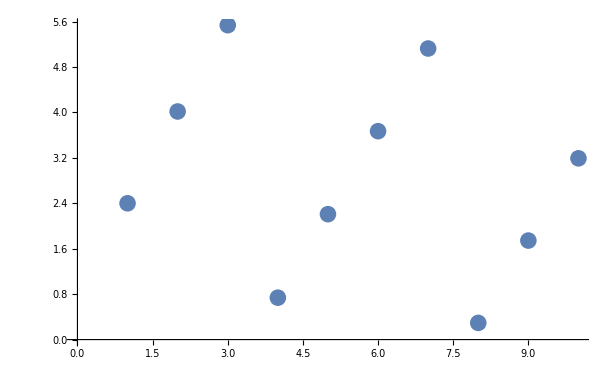

```mathematica
ListPlot[Mod[angle[#,1.33],2Pi]&/@Range[10]]
```

```mathematica
angle[5,1.33]-2Pi
```

2.20802

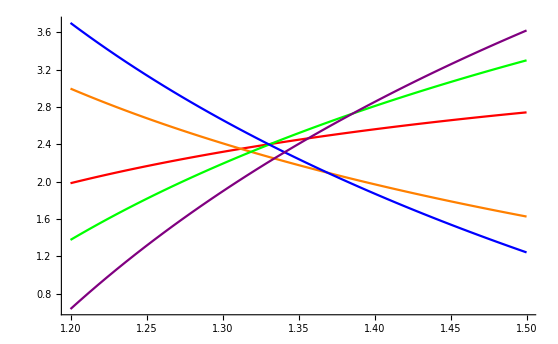

```mathematica
Plot[{angle[1,n],2Pi-angle[2,n],angle[3,n]-Pi,3Pi-angle[4,n],angle[5,n]-2Pi},{n,1.2,1.5},PlotStyle->{Red,Orange,Green,Blue,Purple}]
```

```mathematica
FullSimplify[If[EvenQ[xx],1+xx/2,(1-xx)/2]]
```

(1-xx)/2

```mathematica
fitangle[k_,n_]:=1/4 (3 π+(-1)^k (π+2 k π-4 angle[k,n]))
```

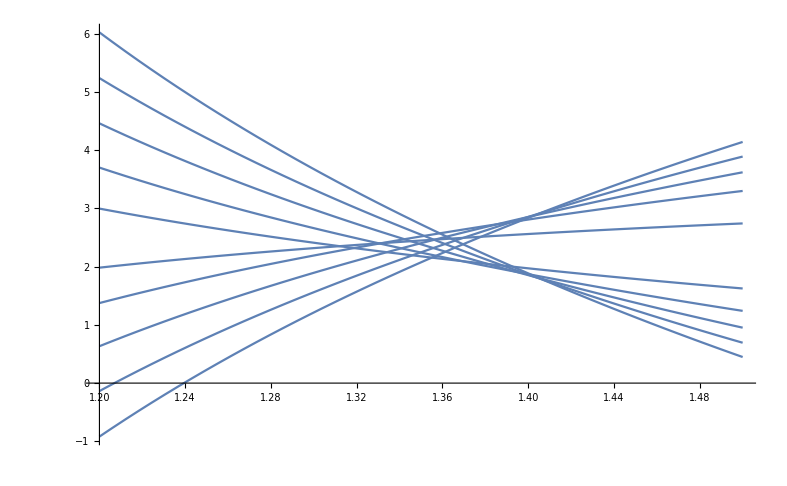

```mathematica
Plot[fitangle[#,n]&/@Range[10],{n,1.2,1.5}]
```

```mathematica
fit[m_]:=90-180/Pi*With[{t=Mod[m,2Pi]+Pi/2},If[t<Pi/2,t,If[t<Pi,Pi-t,-If[t<3Pi/2,t-Pi,2Pi-t]]]]
```

```mathematica
,fit[angle[7,n]],fit[angle[8,n]],fit[angle[9,n]],fit[angle[10,n]]
```

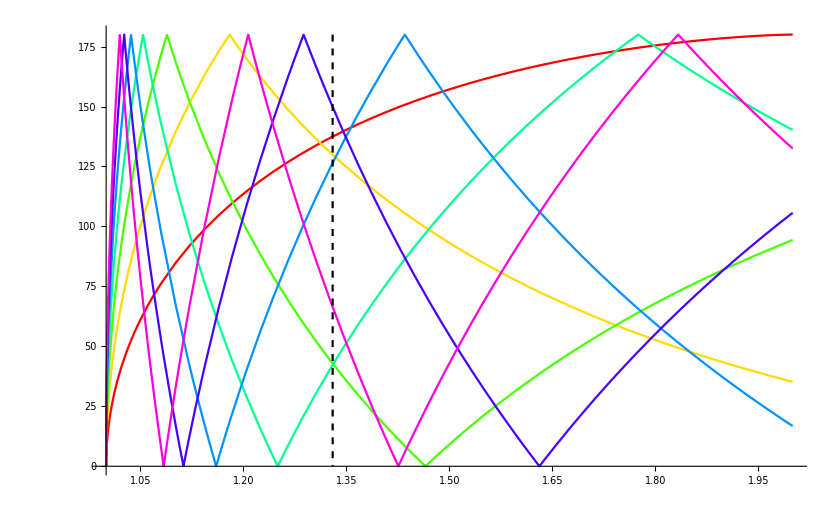

```mathematica
Plot[{fit[angle[1,n]],fit[angle[2,n]],fit[angle[3,n]],fit[angle[4,n]],fit[angle[5,n]],fit[angle[6,n]],fit[angle[7,n]],If[n>1.33,-300,300]},{n,1,2},PlotRange->{0,180},PlotStyle->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,{Dashed,Black}}]
```

```mathematica
Hue/@Range[0,1,1/7]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Abs[Mod[an[#,n],2Pi]-Pi]&/@Range[5]
```

{Abs[-π+Mod[an[1,n],2 π]],Abs[-π+Mod[an[2,n],2 π]],Abs[-π+Mod[an[3,n],2 π]],Abs[-π+Mod[an[4,n],2 π]],Abs[-π+Mod[an[5,n],2 π]]}

```mathematica
Solve[fitangle[2,n]==fitangle[5,n]&&1.3<n<1.4,n]
```

{{n→1.33406}}

```mathematica
1.3340589504554585
```

```mathematica
Solve[fitangle[2,n]==fitangle[1,n]&&1.3<n<1.4,n]
```

{{n→1.31201}}